```mathematica
F[x_]:=ⅇ^(x/π)
```

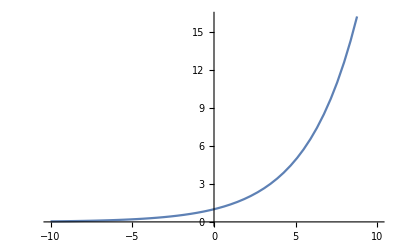

```mathematica
Plot[F[x],{x,-10,10}]
```

```mathematica
h=1;
x={{1},{2},{3}};
y=Flatten@N@Map[F,x]
```

{1.3748,1.89008,2.59849}

```mathematica
n={1,t}
```

{1,t}

```mathematica
delta[x_,k_]:=Sum[(-1)^(x-n)*Binomial[x,n]*y[[n+1+k]],{n,0,x}]
```

```mathematica
P[t_]:=f[x[[1]]]+∑_(n=1)^(Length@x-1) ((t-n+1)*delta[n,0]*∏_(i=n)^n (t-x[[i]]))/(n!*h^n)
```

```mathematica
P[q]
```

{ⅇ^(1/π)+0.0965638 (-2+q) (-1+q)+0.515279 (-1+q) q}

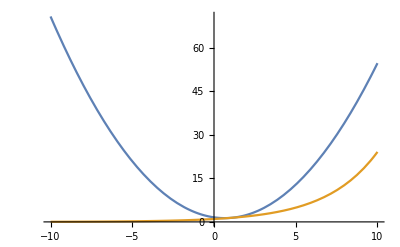

```mathematica
Plot[{P[a],F[a]},{a,-10,10}]
```